```mathematica
simple = Transpose[Import["~/zeca-results-all-cell/zeca-results-all-cell/chameleonic-10/simple/run_10000/tmp"]];
rose = Transpose[Import["~/zeca-results-all-cell/zeca-results-all-cell/chameleonic-10/rose/run_10000/tmp"]];roseSpecial = Transpose[Import["~/zeca-results-all-cell/zeca-results-all-cell/chameleonic-10/rose_special/run_10000/tmp"]];
roseSpecialCharged = Transpose[Import["~/zeca-results-all-cell/zeca-results-all-cell/chameleonic-10/rose_special_charged/run_10000/tmp"]];
```

ListLinePlot::lpn: Transpose[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

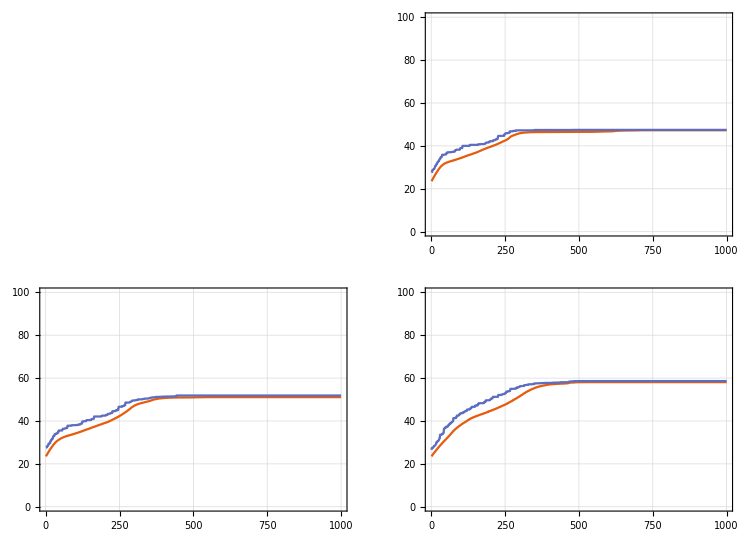

```mathematica
GraphicsGrid[{{ListLinePlot[simple, PlotTheme -> "Scientific", PlotRange-> {{0,1000},{0,100}}, GridLines->Automatic],ListLinePlot[rose, PlotTheme -> "Scientific", PlotRange-> {{0,1000},{0,100}}, GridLines->Automatic]},{ ListLinePlot[roseSpecial, PlotTheme -> "Scientific", PlotRange-> {{0,1000},{0,100}}, GridLines->Automatic], ListLinePlot[roseSpecialCharged, PlotTheme -> "Scientific", PlotRange-> {{0,1000},{0,100}}, GridLines->Automatic]}}]
```

## Q3, Qh, Qe,Qc

```mathematica
simpleQ3 = Flatten[Import["~/zeca-apply-results/chameleonic-10/simple/run_10000/stat_Q3", "Table"]];
simpleQh = Flatten[Import["~/zeca-apply-results/chameleonic-10/simple/run_10000/stat_Qh", "Table"]];
simpleQe = Flatten[Import["~/zeca-apply-results/chameleonic-10/simple/run_10000/stat_Qe", "Table"]];
simpleQc = Flatten[Import["~/zeca-apply-results/chameleonic-10/simple/run_10000/stat_Qc", "Table"]];
roseQ3 = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose/run_10000/stat_Q3", "Table"]];
roseQh = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose/run_10000/stat_Qh", "Table"]];
roseQe = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose/run_10000/stat_Qe", "Table"]];
roseQc = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose/run_10000/stat_Qc", "Table"]];
roseSpecialQ3 = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special/run_10000/stat_Q3", "Table"]];
roseSpecialQh = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special/run_10000/stat_Qh", "Table"]];
roseSpecialQe = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special/run_10000/stat_Qe", "Table"]];
roseSpecialQc = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special/run_10000/stat_Qc", "Table"]];
roseSpecialChargedQ3 = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special_charged/run_10000/stat_Q3", "Table"]];
roseSpecialChargedQh = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special_charged/run_10000/stat_Qh", "Table"]];
roseSpecialChargedQe = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special_charged/run_10000/stat_Qe", "Table"]];
roseSpecialChargedQc = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special_charged/run_10000/stat_Qc", "Table"]];
```

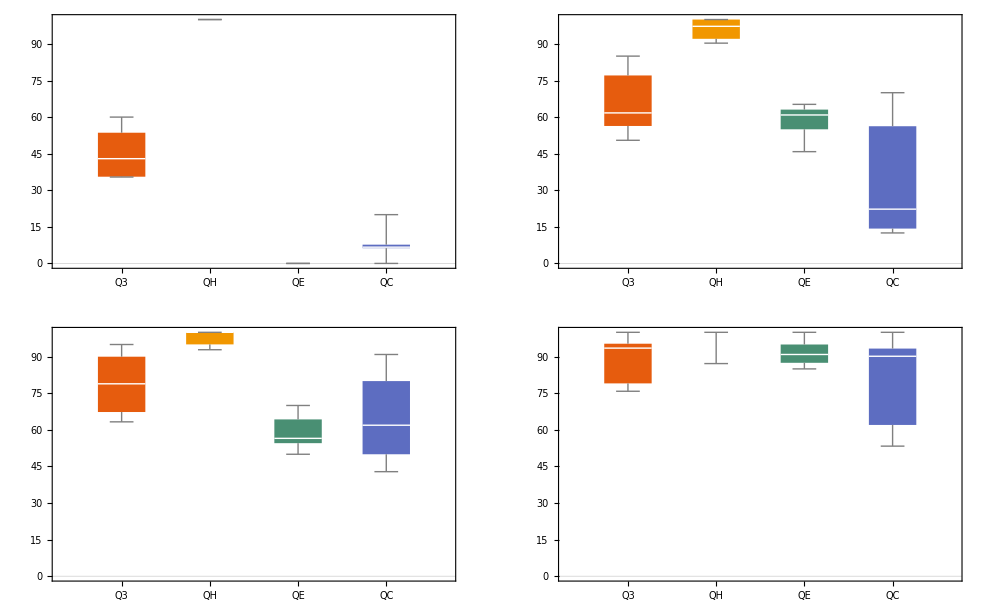

```mathematica
GraphicsGrid[{{BoxWhiskerChart[{{simpleQ3, simpleQh,simpleQe, simpleQc}}, ChartLabels->{"Q3", "QH", "QE","QC"}, PlotTheme->"Scientific", PlotRange->{0,100}],BoxWhiskerChart[{{roseQ3, roseQh,roseQe, roseQc}}, ChartLabels->{"Q3", "QH", "QE","QC"}, PlotTheme->"Scientific", PlotRange->{0,100}]},{BoxWhiskerChart[{{roseSpecialQ3, roseSpecialQh,roseSpecialQe, roseSpecialQc}}, ChartLabels->{"Q3", "QH", "QE","QC"}, PlotTheme->"Scientific", PlotRange->{0,100}],BoxWhiskerChart[{{roseSpecialChargedQ3, roseSpecialChargedQh,roseSpecialChargedQe, roseSpecialChargedQc}}, ChartLabels->{"Q3", "QH", "QE","QC"}, PlotTheme->"Scientific", PlotRange->{0,100}]}}]
```

## Q3, Qh, Qe, Qc - bad

```mathematica
simpleQ3Bad = Flatten[Import["~/zeca-apply-results/chameleonic-10/simple/run_10000/stat_Q3_bad", "Table"]];
simpleQhBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/simple/run_10000/stat_Qh_bad", "Table"]];
simpleQeBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/simple/run_10000/stat_Qe_bad", "Table"]];
simpleQcBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/simple/run_10000/stat_Qc_bad", "Table"]];
roseQ3Bad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose/run_10000/stat_Q3_bad", "Table"]];
roseQhBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose/run_10000/stat_Qh_bad", "Table"]];
roseQeBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose/run_10000/stat_Qe_bad", "Table"]];
roseQcBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose/run_10000/stat_Qc_bad", "Table"]];
roseSpecialQ3Bad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special/run_10000/stat_Q3_bad", "Table"]];
roseSpecialQhBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special/run_10000/stat_Qh_bad", "Table"]];
roseSpecialQeBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special/run_10000/stat_Qe_bad", "Table"]];
roseSpecialQcBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special/run_10000/stat_Qc_bad", "Table"]];
roseSpecialChargedQ3Bad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special_charged/run_10000/stat_Q3_bad", "Table"]];
roseSpecialChargedQhBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special_charged/run_10000/stat_Qh_bad", "Table"]];
roseSpecialChargedQeBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special_charged/run_10000/stat_Qe_bad", "Table"]];
roseSpecialChargedQcBad = Flatten[Import["~/zeca-apply-results/chameleonic-10/rose_special_charged/run_10000/stat_Qc_bad", "Table"]];
```

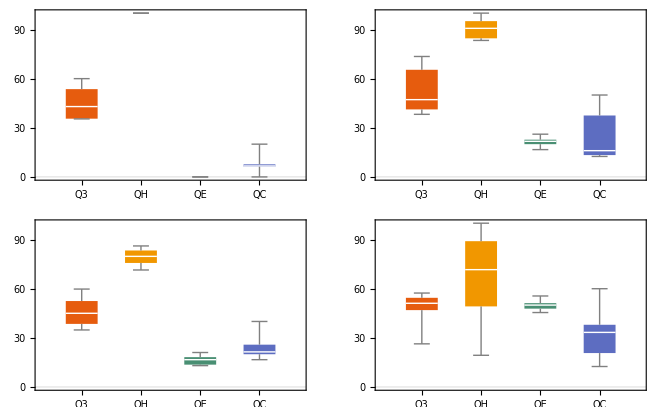

```mathematica
GraphicsGrid[{{BoxWhiskerChart[{{simpleQ3Bad, simpleQhBad,simpleQeBad, simpleQcBad}}, ChartLabels->{"Q3", "QH", "QE","QC"}, PlotTheme->"Scientific", PlotRange->{0,100}],BoxWhiskerChart[{{roseQ3Bad, roseQhBad,roseQeBad, roseQcBad}}, ChartLabels->{"Q3", "QH", "QE","QC"}, PlotTheme->"Scientific", PlotRange->{0,100}]},{BoxWhiskerChart[{{roseSpecialQ3Bad, roseSpecialQhBad,roseSpecialQeBad, roseSpecialQcBad}}, ChartLabels->{"Q3", "QH", "QE","QC"}, PlotTheme->"Scientific", PlotRange->{0,100}],BoxWhiskerChart[{{roseSpecialChargedQ3Bad, roseSpecialChargedQhBad,roseSpecialChargedQeBad, roseSpecialChargedQcBad}}, ChartLabels->{"Q3", "QH", "QE","QC"}, PlotTheme->"Scientific", PlotRange->{0,100}]}}]
```

```mathematica
data0 = TemporalData[{1,1,1,0,0,1,2,1,0,0},{Range[10]}, ResamplingMethod->None]
```

TemporalData[…]

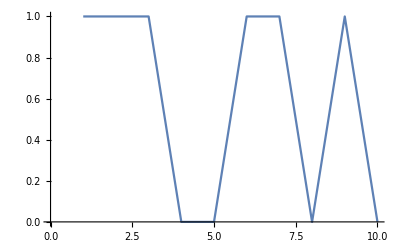

```mathematica
ListLinePlot[data]
```

```mathematica
eproc= EstimatedProcess[data,DiscreteMarkovProcess[1]]
```

EstimatedProcess::ntsprt: One or more data points are not in the support of the process DiscreteMarkovProcess[{p[1]},{{s[1,1]}}].

EstimatedProcess[{1,0,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,1,1,1,0,0,0,1,1,0,1,0},DiscreteMarkovProcess[1]]

```mathematica
eproc
```

EstimatedProcess[{1,0,1,1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,0,1,0,1,1,1,0,0,0,1,1,0,1,0},DiscreteMarkovProcess[1]]

```mathematica
𝒫=DiscreteMarkovProcess[3,{{1/2,1/2,0,0},{1/2,1/2,0,0},{1/4,1/4,1/4,1/4},{0,0,0,1}}];
```

```mathematica
data=RandomFunction[𝒫,{0,10^4},1];
```

```mathematica
data
```

TemporalData[…]

```mathematica
ListLinePlot[data[[100]]]
```

Part::partw: Part 100 of TemporalData[Automatic,{{{3,2,2,1,1,2,1,2,1,1,1,1,1,1,2,2,2,1,2,1,1,2,2,1,2,1,2,1,2,2,1,2,1,1,1,1,2,2,1,2,2,1,2,1,1,1,2,2,1,1,«9951»}},{{0,10000,1}},1,{Discrete,1},{Discrete,1},1,{ValueDimensions→1,ResamplingMethod→None}},False,11.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: TemporalData[Automatic,{{{3,2,2,1,1,2,1,2,1,1,1,1,1,1,2,2,2,1,2,1,1,2,2,1,2,1,2,1,2,2,1,2,1,1,1,1,2,2,1,2,2,1,2,1,1,1,2,2,1,1,«9951»}},{{0,10000,1}},1,{Discrete,1},{Discrete,1},1,{ValueDimensions→1,ResamplingMethod→None}},False,11.]⟦100⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[TemporalData[…]⟦100⟧]

```mathematica
Map[MatrixForm,estproc=EstimatedProcess[data0,DiscreteMarkovProcess[3],WorkingPrecision->MachinePrecision]]
```

EstimatedProcess::ntsprt: One or more data points are not in the support of the process DiscreteMarkovProcess[{p[1],p[2],p[3]},{{s[1,1],s[1,2],s[1,3]},{s[2,1],s[2,2],s[2,3]},{s[3,1],s[3,2],s[3,3]}}].

General::invldd: The input data … should be a vector or a matrix of real numbers or a valid TemporalData object.

EstimatedProcess[TemporalData[…],DiscreteMarkovProcess[3],WorkingPrecision→MachinePrecision]